## Numerical Results for Neutrino Oscillations in Matter

### Prep

```mathematica
SetDirectory@NotebookDirectory[]
```

/Users/leima/Dropbox/Research/git/15summer/assets

```mathematica
ClearAll[deltaH,numDen]
```

### Numerical

First of all I need to construct the function of solar electron number density.

#### Define Interpolation Function

```mathematica
numDen[x_]=10^(-14-4.3 x)
```

10^(-14-4.3 x)

```mathematica
numDen[0]
```

1.×10^-14

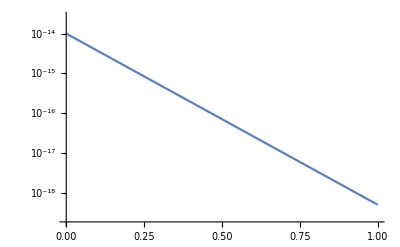

```mathematica
LogPlot[numDen[x],{x,0,1}]
```

Some useful constants
Fermi coupling constant G_F /(hbar c)    1.166 378 7(6)×10^−5 GeV−2

```mathematica
rS = 10^5;
omega=10^(-19);
(*rSomega=rS*omega;*)
rSomega=1
gF=1.17*10^(-5);
deltaH[x_] = Sqrt[2]gF numDen[x]/(omega)
thetaV=Pi/6;
```

1

0.0000165463 10^(5-4.3 x)

Hamiltonian is

```mathematica
hamilM[x_]=rSomega/2{{deltaH[x]-Cos[2thetaV],Sin[2thetaV]},{Sin[2thetaV],-deltaH[x]+Cos[2thetaV]}}
```

{{1/2 (-1/2+0.0000165463 10^(5-4.3 x)),(√3)/4},{(√3)/4,1/2 (1/2-0.0000165463 10^(5-4.3 x))}}

The function to be obtained is

```mathematica
nuM[x_]={nuMe[x],nuMx[x]}
```

{nuMe[x],nuMx[x]}

The system becomes

```mathematica
matOsc=I nuM'[x]==hamilM[x].nuM[x]
```

{ⅈ nuMe'[x],ⅈ nuMx'[x]}=={1/2 (-1/2+0.0000165463 10^(5-4.3 x)) nuMe[x]+1/4 √3 nuMx[x],1/4 √3 nuMe[x]+1/2 (1/2-0.0000165463 10^(5-4.3 x)) nuMx[x]}

```mathematica
solM=NDSolve[matOsc&&nuM[0]=={1,0},{nuMe,nuMx},{x,0,1}]
```

{{nuMe→InterpolatingFunction[{{0., 1.}}, <>],nuMx→InterpolatingFunction[{{0., 1.}}, <>]}}

```mathematica
probesqrt=nuMe/.solM[[1]]
probxsqrt=nuMx/.solM[[1]]
```

InterpolatingFunction[{{0., 1.}}, <>]

InterpolatingFunction[{{0., 1.}}, <>]

```mathematica
Table[probesqrt[i],{i,0,1,0.1}]
probxsqrt[0]
```

{1.+0. ⅈ,0.998684-0.0275005 ⅈ,0.996011-0.0219835 ⅈ,0.991567-0.00420617 ⅈ,0.984882+0.0180998 ⅈ,0.975791+0.0420301 ⅈ,0.964268+0.0664709 ⅈ,0.950332+0.0909721 ⅈ,0.934017+0.115329 ⅈ,0.915365+0.139428 ⅈ,0.894424+0.163189 ⅈ}

0.+0. ⅈ

```mathematica
norm[x_]=Abs[probesqrt[x]]^2+Abs[probxsqrt[x]]^2
```

Abs[InterpolatingFunction[{{0., 1.}}, <>][x]]^2+Abs[InterpolatingFunction[{{0., 1.}}, <>][x]]^2

```mathematica
Table[norm[i],{i,0,1,0.1}]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

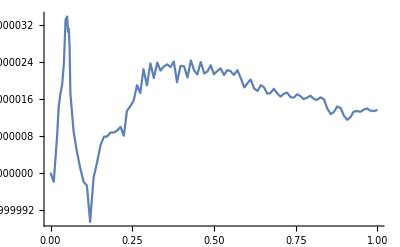

```mathematica
Plot[norm[x],{x,0,1}]
```

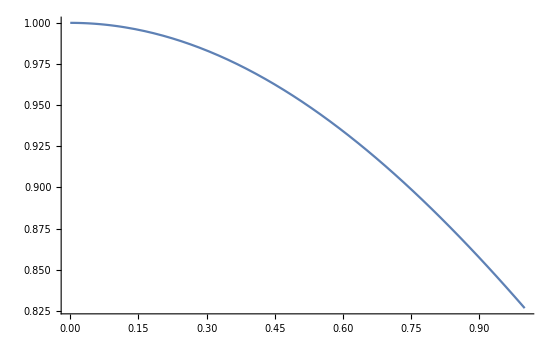

```mathematica
Plot[Abs[probesqrt[x]]^2/norm[x],{x,0,1}]
```

```mathematica
Abs[probesqrt[x]]^2
```

Abs[InterpolatingFunction[{{0., 1.}}, <>][x]]^2